```mathematica
summary=SemanticImport[FileNameJoin@{NotebookDirectory[],"list3.2.xls"}];
```

```mathematica
summary=summary[All,;;8]//Dataset
```

Dataset[<>]

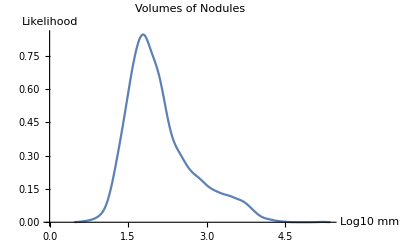

```mathematica
volume=SmoothHistogram[Log10/@summary[All,"volume"],AxesLabel->{"Log10 mm^3","Likelihood"},PlotLabel->"Volumes of Nodules"]
```

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"volumes.pdf"},volume]
```

C:\Users\lhe\cs109b\cs109b-projectofchampions\data\volumes.pdf

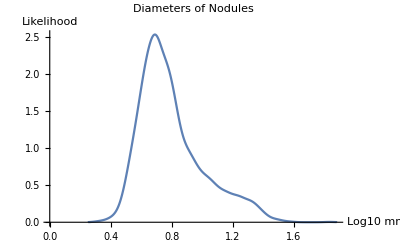

```mathematica
diameter=SmoothHistogram[Log10/@summary[All,"eq. diam."],AxesLabel->{"Log10 mm","Likelihood"},PlotLabel->"Diameters of Nodules"]
```

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"diameters.pdf"},diameter]
```

C:\Users\lhe\cs109b\cs109b-projectofchampions\data\diameters.pdf

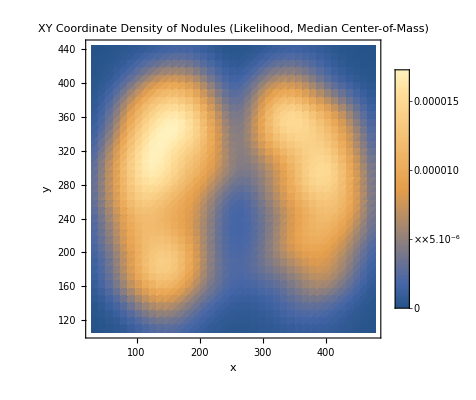

```mathematica
loc=SmoothDensityHistogram[Values/@summary[All,{"x loc.","y loc."}],FrameLabel->{"x","y"},PlotLabel->"XY Coordinate Density of Nodules\n(Likelihood, Median Center-of-Mass)",PlotLegends->Automatic]
```

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"locs.pdf"},loc]
```

C:\Users\lhe\cs109b\cs109b-projectofchampions\data\locs.pdf

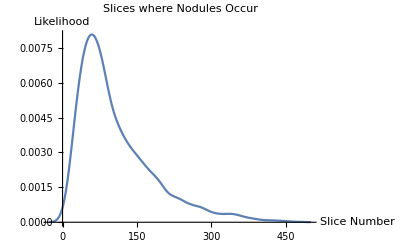

```mathematica
slice=SmoothHistogram[summary[All,"slice no."],AxesLabel->{"Slice Number","Likelihood"},PlotLabel->"Slices where Nodules Occur"]
```

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"slices.pdf"},slice]
```

C:\Users\lhe\cs109b\cs109b-projectofchampions\data\slices.pdf

```mathematica
noduleCounts=SemanticImport[FileNameJoin@{NotebookDirectory[],"lidc-idri nodule counts (6-23-2015).xlsx"}];
```

```mathematica
noduleCounts=noduleCounts[All,;;4]//Dataset
```

Dataset[<>]

```mathematica
Counts[noduleCounts[All,"Total Number of Nodules*"]]//KeySort
```

Dataset[<>]

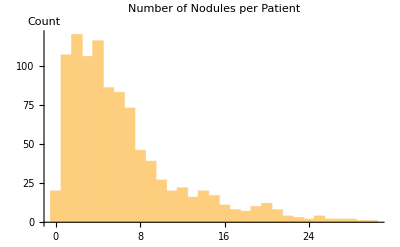

```mathematica
nodules=Histogram[Select[noduleCounts[All,"Total Number of Nodules*"],LessEqualThan[30]],AxesLabel->{None,"Count"},PlotRange->Full,PlotLabel->"Number of Nodules per Patient"]
```

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"nodules.pdf"},nodules]
```

C:\Users\lhe\cs109b\cs109b-projectofchampions\data\prelim_EDA\nodules.pdf

```mathematica
Counts[noduleCounts[All,"Number of Nodules >=3mm**"]]//KeySort
```

Dataset[<>]

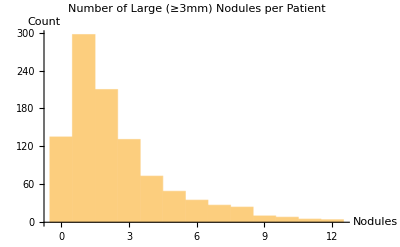

```mathematica
nodulesLarge=Histogram[Select[noduleCounts[All,"Number of Nodules >=3mm**"],LessEqualThan[12]],{1},AxesLabel->{"Nodules","Count"},PlotLabel->"Number of Large (≥3mm) Nodules per Patient"]
```

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"nodules_large.pdf"},nodulesLarge]
```

C:\Users\lhe\cs109b\cs109b-projectofchampions\data\prelim_EDA\nodules_large.pdf

```mathematica
Counts[noduleCounts[All,"Number of Nodules <3mm***"]]//KeySort
```

Dataset[<>]

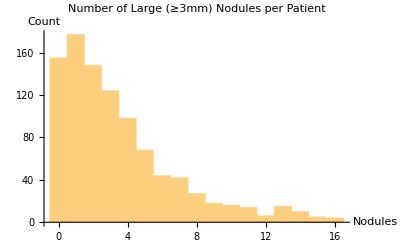

```mathematica
nodulesSmall=Histogram[Select[noduleCounts[All,"Number of Nodules <3mm***"],LessEqualThan[16]],{1},AxesLabel->{"Nodules","Count"},PlotLabel->"Number of Large (≥3mm) Nodules per Patient"]
```

```mathematica
Export[FileNameJoin@{NotebookDirectory[],"nodules_small.pdf"},nodulesSmall]
```

C:\Users\lhe\cs109b\cs109b-projectofchampions\data\prelim_EDA\nodules_small.pdf